Polygon[…]

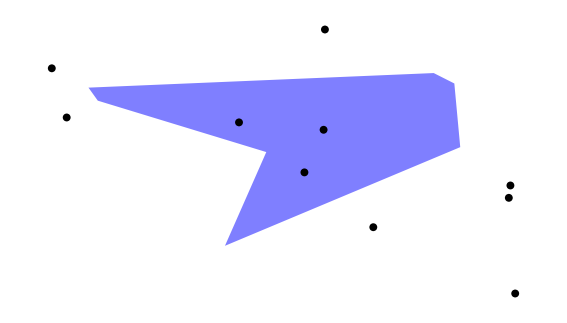

```mathematica
file= Import["C:\\Users\\gerce\\WORK DIRECTORY\\ПРАКТИКА 3 сем\\ЧТОТО ГОТОВОЕ\\КОД\\problem.txt","Table"];
n=file[[1,1]]  (*кол-во исследуемых точек *);
pn= file[[(n+1)+1,1]](*кол-во вершин многоугольника*);
PolMas=Take[file, {n+3,n+2+pn}](*список вершин*);
P = Take[file,{2,n+1}] (*список исследуемых точек*);
Pol=Polygon[PolMas]

Graphics[{FaceForm[{Opacity[0.5],Cyan}],Blue,Polygon[PolMas],Black,PointSize[0.01],Point[Table[P[[i]],{i,1,n}]]}]
```

```mathematica
res1=Select[P, RegionMember[Pol,#]==True &] (*Использование встроенной функции RegionMember*)
F[point_List]:= (*Метод сумирования углов*)
VectorAngle[(PolMas[[pn]]-point),(PolMas[[1]]-point)]*Sign[Det[{(PolMas[[pn]]-point),(PolMas[[1]]-point)}]]+∑_(i=1)^(pn-1) (VectorAngle[(PolMas[[i]]-point),(PolMas[[i+1]]-point)]*Sign[Det[{(PolMas[[i]]-point),(PolMas[[i+1]]-point)}]]);

res2=Select[P,(Abs[F[#]]==2π)&]
```

{{0.464358,0.271586},{-0.415841,0.34859},{0.264953,-0.171982}}

{{0.464358,0.271586},{-0.415841,0.34859},{0.264953,-0.171982}}

```mathematica
(*В пространстве*)

file2= Import["C:\\Users\\gerce\\WORK DIRECTORY\\ПРАКТИКА 3 сем\\ЧТОТО ГОТОВОЕ\\КОД\\problem3D.txt","Table"];
n2=file2[[1,1]]  (*кол-во исследуемых точек *);
pn2= file2[[(n2+1)+1,1]](*кол-во вершин многоугольника*);
PolMas2=Take[file2, {n2+3,n2+2+pn2}](*список вершин*);
P2 = Take[file2,{2,n2+1}] (*список исследуемых точек*);
Pol2=Polygon[PolMas2];
Graphics3D[{Opacity[.64],Pol2,Opacity[1], Black,PointSize[0.01],Point[Table[P2[[i]],{i,1,n}]]}]
```

-Graphics3D-

```mathematica
res13d=Select[P2, RegionMember[Pol2,#]==True &] (*Использование встроенной функции RegionMember*)

F3D[point_List]:= 
VectorAngle[(PolMas2[[pn2]]-point-Projection[PolMas2[[pn2]]-point,{0,0,1}]),(PolMas2[[1]]-point-Projection[PolMas2[[1]]-point,{0,0,1}])]*Sign[((PolMas2[[pn2]]-point-Projection[PolMas2[[pn2]]-point,{0,0,1}])×(PolMas2[[1]]-point-Projection[PolMas2[[1]]-point,{0,0,1}]))[[3]]]+∑_(i=1)^(pn-1) VectorAngle[(PolMas2[[i]]-point-Projection[PolMas2[[i]]-point,{0,0,1}]),(PolMas2[[i+1]]-point-Projection[PolMas2[[i+1]]-point,{0,0,1}])]*Sign[((PolMas2[[i]]-point-Projection[PolMas2[[i]]-point,{0,0,1}])×(PolMas2[[i+1]]-point-Projection[PolMas2[[i+1]]-point,{0,0,1}]))[[3]]];

(*re=Select[projectionPoint,(Abs[F3D[#]]==2π)&]*)
point2={3,5,4};
Projection[(PolMas2[[1]]-point2-Projection[PolMas2[[1]]-point2,{0,0,1}])*(PolMas2[[pn]]-point2-Projection[PolMas2[[pn]]-point2,{0,0,1}]),{0,0,1}];

res23d=Select[P2,(Abs[F3D[#]]==2π)&]
```

{{-0.182445,-0.17203,0.0143319},{0.195773,0.17604,-0.0107356}}

{{-0.182445,-0.17203,0.0143319},{0.195773,0.17604,-0.0107356}}

{{-0.182445,-0.17203,0.0143319},{0.195773,0.17604,-0.0107356}}